```mathematica
Print[Button[Style["Quit Kernel",Bold],Quit[],ImageSize->{150,35}]]
```

Quit Kernel

Regressive Näherung von Daten (Messdatenreihe oder diskretisierte Funktion) durch möglichst einfache nicht periodische Funktion ϕ(x). Im folgenden Programm wird eine nach dem n_-/n_+-ten Glied abgebrochene Laurent-Reihe verwendet:

ϕ[x]=∑_(i=-n_-)^(n_+) c_i·x^i

Für n_-<0 darf in den Daten kein Punkt an der Stelle x=0 vorhanden sein.
Für n_-=0 vereinfacht sich diese zu einer nach dem n-ten Glied abgebrochene Mac-Laurin-Reihe bzw. Taylor-Reihe:

ϕ[x]=∑_(i=0)^n c_i·x^i

Für n=0 ergibt sich der Mittelwert der Daten.
Es resultiert ein überbestimmtes Gleichungssystem, woraus sich folgende Bedingung ableiten lässt:

Anzahl  der Datenpunkte > Anzahl der Summanden von ϕ(x)

## Eingabe (𝒹𝒶𝓉ℯ𝓃)

```mathematica
ClearAll["Global`*"]
𝒹𝒶𝓉ℯ𝓃={{1.0246370932624713,12.193196747933298},{0.8312102019555705,7.591372429117404},{0.6907583245367346,8.411547956677362},{0.882318553165916,11.744978868636403},{1.2199383327839932,15.62361811212518},{1.1165872426690646,20.211325436148144},{2.0536738526243767,25.501583077420275},{2.4592715950985835,31.310885562855525},{2.651489921465937,38.18790042515198},{2.532385582966854,45.98908464651669},{2.559173796723091,53.954241483301175},{2.7870737012340596,63.05568354603591},{2.544318462736392,73.28405648064226},{3.2418651055061662,84.07940904008814},{3.398387612797225,94.90926370667748},{3.183863267821115,107.01710322673412},{3.3264893773548967,120.08579258842175},{3.9450028854043424,132.99048024693235},{4.101773438403658,147.18471327297647},{4.062527240825606,162.2533959841616},{4.1467222415861045,177.8024509514607},{4.893096667364441,194.4296083892699},{4.592659048542803,211.35981667859215},{5.233539190099422,229.03185609978442},{5.235219927020713,247.12423016324328},{5.326977338566095,266.63162215676635},{6.073810620058696,286.49878564879504},{6.49241717967837,307.2732621064613},{5.963697417104401,328.0507760281935},{6.735965247147869,350.8395497401225},{6.287694645307145,373.38279165448597},{6.909364203001523,396.93185181408023},{7.468065757623157,420.94838484491555},{6.73779339405677,445.378640743621},{7.581352854584551,471.36368708609217}};
```

## Plot

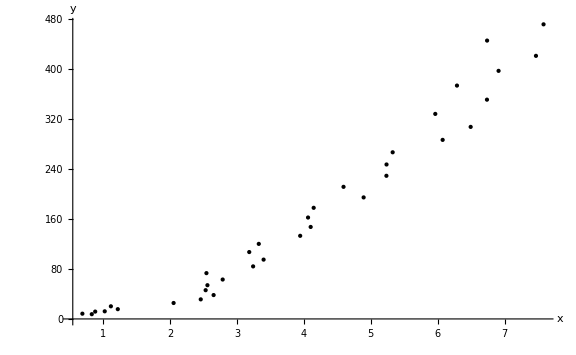

```mathematica
(*Ausgabe*)
plotDaten=ListPlot[𝒹𝒶𝓉ℯ𝓃,
PlotStyle->{Black,PointSize->Medium},AxesLabel->{"x","y"},PlotRange->All,ImageSize->Large];
Print[Show[plotDaten]]
```

## Programm (automatisch)

```mathematica
𝓃={0,3};
```

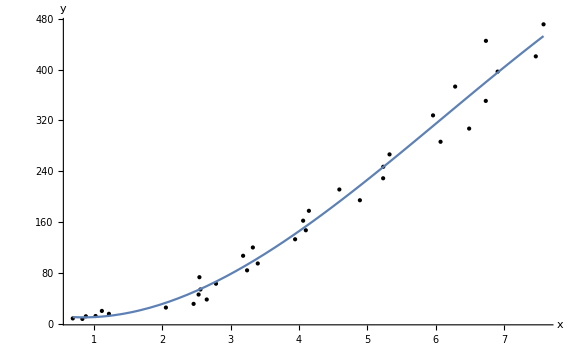

ϕ(x) = 22.8854-31.0274 x+19.7233 x^2-1.07498 x^3
ρ = 21.0467

```mathematica
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Table[x^i,{i,𝓃[[1]],𝓃[[2]]}];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

## Programm (manuell)

```mathematica
𝓃={0,3};
```

```mathematica
(*Programm*)
𝒜=Table[If[j==0,1,𝒹𝒶𝓉ℯ𝓃[[i,1]]]^j,{i,Length[𝒹𝒶𝓉ℯ𝓃]},{j,𝓃[[1]],𝓃[[2]]}];
𝒷=𝒹𝒶𝓉ℯ𝓃[[All,2]];
𝒸=LeastSquares[𝒜,𝒷];
ϕ[x_]=Sum[𝒸[[i+1+Abs[𝓃[[1]]]]] x^i,{i,𝓃[[1]],𝓃[[2]]}];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],
Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},PlotRange->All];
Print[Show[plotDaten,plot,PlotRange->All]]
Print[StringForm["ϕ(x) = ``\nρ = ``",ϕ[x],ρ]]
```

-Graphics-

ϕ(x) = 22.8854-31.0274 x+19.7233 x^2-1.07498 x^3
ρ = 21.0467

## Programm (Vergleich)

```mathematica
𝓃={0,6};
```

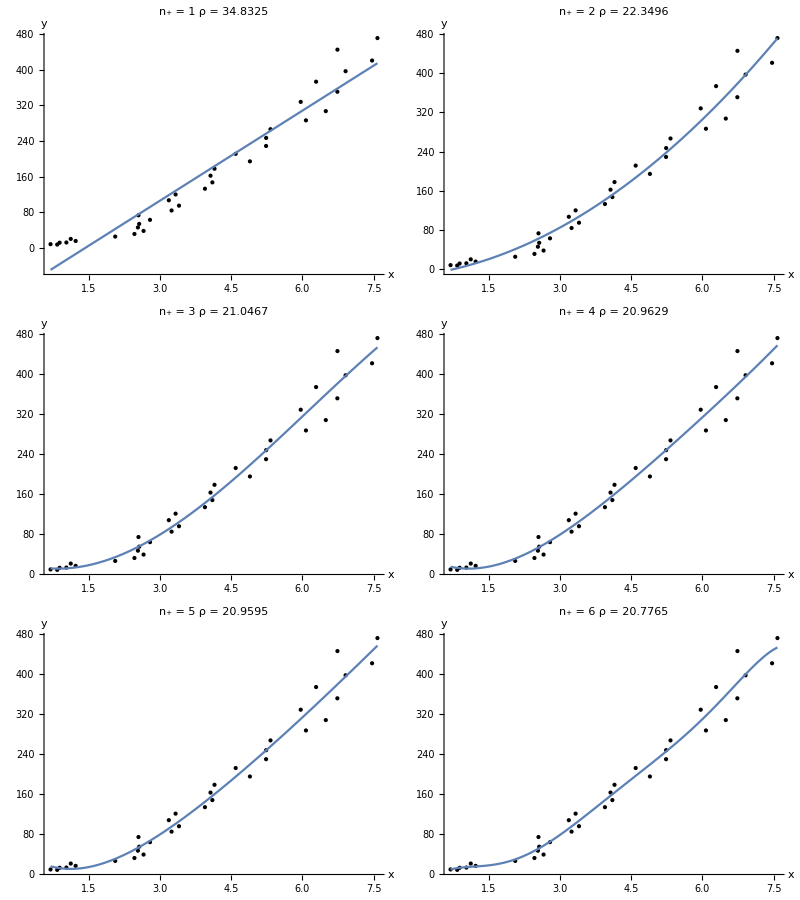

```mathematica
Print[TableForm[Partition[Table[
(*Programm*)
𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃=Table[x^i,{i,𝓃[[1]],j}];
ϕ[x_]=Fit[𝒹𝒶𝓉ℯ𝓃,𝒻𝓊𝓃𝓀𝓉𝒾ℴ𝓃ℯ𝓃,x];
ρ=√(1/Length[𝒹𝒶𝓉ℯ𝓃] Sum[(𝒹𝒶𝓉ℯ𝓃[[i,2]]-ϕ[𝒹𝒶𝓉ℯ𝓃[[i,1]]])^2,{i,Length[𝒹𝒶𝓉ℯ𝓃]}]);

(*Ausgabe*)
plot=Plot[ϕ[x],
{x,Min[𝒹𝒶𝓉ℯ𝓃[[All,1]]],Max[𝒹𝒶𝓉ℯ𝓃[[All,1]]]},
PlotRange->All];
Show[plotDaten,plot,PlotRange->All,PlotLabel->StringForm["n_+ = ``\nρ = ``",j,ρ],ImageSize->Medium]
,{j,If[Mod[𝓃[[2]],2]==0,𝓃[[2]],𝓃[[2]]+1]}],2]]]
```